```mathematica
Ggauss[q_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}],{k,1,100}];
```

```mathematica
Cascade2single[z_, r_] = (SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[Ggauss[q,  z, r], {q, 0,2}],0]*SeriesCoefficient[Series[Ggauss[q, z, r], {q, 0,2}],2]);
```

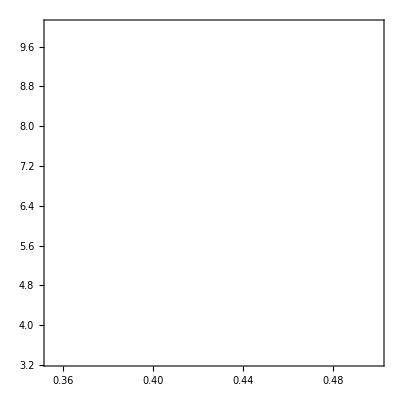

```mathematica
single = ContourPlot[(Cascade2single[z, r])==0, {r, 0.3543, 0.5}, {z,3.316,10}, ContourStyle->Directive[RGBColor[1.,1.,1.]]]
```

```mathematica
GE1gauss[q_, p_, z_, r_] = Sum[PDF[PoissonDistribution[z],k]*k/z*Sum[PDF[BinomialDistribution[k-1,q],m]*CDF[NormalDistribution[r,0.2],m/k], {m, 0, k-1}]*Sum[PDF[BinomialDistribution[k,p],w]*CDF[NormalDistribution[r,0.2],w/k], {w, 0, k}],{k,1,100}]
```

1/2 ⅇ^-z Erfc[3.53553 r] (1/2 p Erfc[3.53553 (-1+r)]+1/2 (1-p) Erfc[3.53553 r])+98+(ⅇ^-z 2 (1/2 q^99 Erfc[3.53553 (-99/100+r)]+98+1/2 1^99 Erfc[18 r]))/(9332621544394415268169923885626670049071596826438162526979208272237582511852109168640000000000000000000000)
 |  |  |  |

```mathematica
CascadeEdge2[z_, r_] = (SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],1]-1)^2 - 4*(SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],0]*SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,2}],2]);
```

```mathematica
Cascade4[z_, r_] = SeriesCoefficient[Series[GE1gauss[q, q, z, r], {q, 0,4}],4]
```

1/16 ⅇ^-z z^4 (10 Erfc[3.53553 (-2/5+r)]^2+10 Erfc[3.53553 (-3/5+r)] Erfc[3.53553 (-1/5+r)]-70 Erfc[3.53553 (-2/5+r)] Erfc[3.53553 (-1/5+r)]+7+21 Erfc[3.53553 r]^2)+96+1/2 ⅇ^1 1 (1/2 (Erfc[3.53553 (-1/3+r)]-Erfc[1]) (1)+3/4 1)
 |  |  |  |

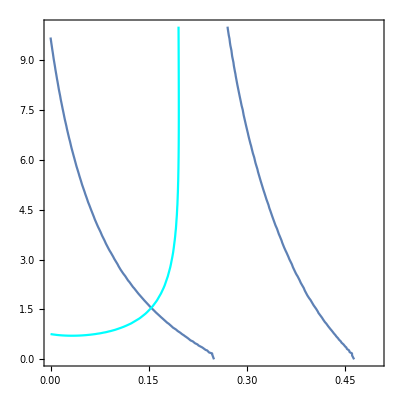

```mathematica
Show[%33, EdgeDouble]
```

```mathematica
FindRoot[{CascadeEdge2[z, r]==0 ,Cascade4[z,r]==0},{{r,0.15},{z,2}}]
```

{r→0.154101,z→1.548}

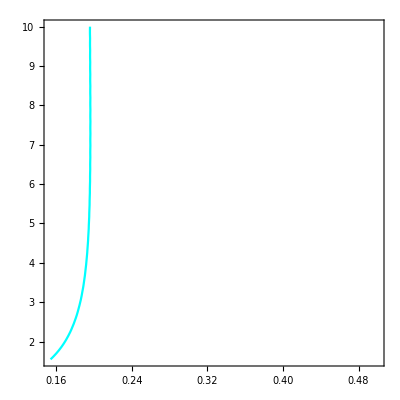

```mathematica
EdgeDouble = ContourPlot[(CascadeEdge2[z, r])==0 , {r, 0.154101, 0.5}, {z,1.548,10}, ContourStyle->Directive[RGBColor[0.,1.,1.]]]
```

```mathematica
data=BinaryReadList["/home/user/Documents/BT_MP/BT_MP/coordination_game/simulations/edge_swap_sim.dat","Real32"];
```

```mathematica
Length[data]
```

420

```mathematica
griddat = ArrayReshape[data, {20, 21}];
```

```mathematica
zcoord = Range[0.5, 10, 0.5];
```

```mathematica
Length[zcoord]
```

20

```mathematica
rcoord = Range[0, 0.4, 0.02];
```

```mathematica
Length[rcoord]
```

21

```mathematica
Surface= Flatten[Table[{rcoord[[j]],zcoord[[i]],griddat[[i,j]]},{j,21},{i,20}],1];
```

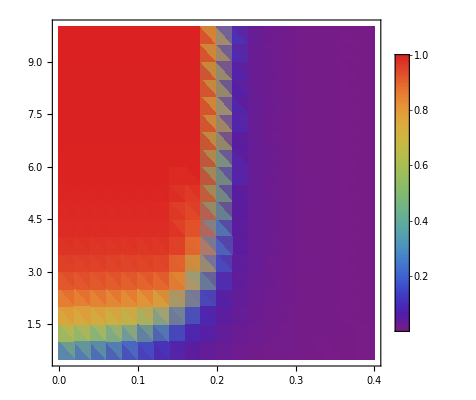

```mathematica
simulationdata = ListDensityPlot[Surface, ColorFunction->"Rainbow", PlotLegends->Automatic, ColorFunctionScaling->False]
```

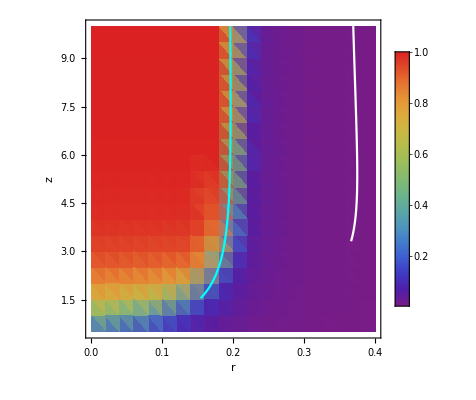

```mathematica
Finaldiagram = Show[simulationdata, single, EdgeDouble , FrameLabel->{{HoldForm[z],None},{HoldForm[r],None}},LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/er_edge.eps",Finaldiagram]
```

~/Documents/BT_MP/BT_MP/MP_doc_templates/new_figs/er_edge.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["er_hetero_edge.eps"]]]
```